Q1: Find the first three roots of the Bessel function J_1(x).

As suggested, plot the first to get an idea

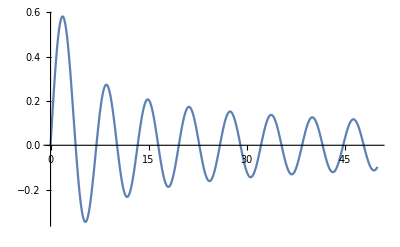

```mathematica
Plot[BesselJ[1,x], {x, 0, 50}]
```

The first three roots should be between 0 and 10 (assuming 0 also counts)

```mathematica
NSolve[BesselJ[1,x]==0 && 0 <=x<=10]
```

{{x→0.},{x→3.83171},{x→7.01559}}

Q3: Solve the equation  x ln(x) - 3 x + 10 = 6, both symbolically and numerically.

```mathematica
f[x_] := x Log[x]-3 x + 10 -6
```

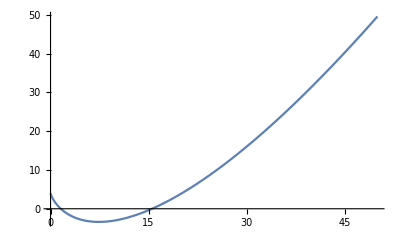

```mathematica
Plot[f[x], {x, 0, 50}]
```

So we should expect to find two roots

```mathematica
FullSimplify[f[x]==0]
```

4+x Log[x]==3 x

```mathematica
Solve[f[x]== 0, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-4/ProductLog[-4/ⅇ^3]},{x→-4/ProductLog[-1,-4/ⅇ^3]}}

ProductLog[z] is a function that gives the principal solution for to  w in z=we^w, and  ProductLog[k,z] is the kth solution. The principal solution, which is when there is no order in the input, is for k=0. Bottom line is, there are indeed two roots, let’s evaluate them numerically

```mathematica
FindRoot[f[x]== 0, {x, 2.2}]
```

{x→1.56883}

With this initial guess only one root is recovered. Let us try and substitute the value in the initial equation and see what we get.

```mathematica
%% /. {x->1.56883}
```

{{1.56883→-4/ProductLog[-4/ⅇ^3]},{1.56883→-4/ProductLog[-1,-4/ⅇ^3]}}

Again, two roots

```mathematica
FindRoot[f[x]==0, {x, -1.5}]
```

{x→1.56883+7.93915×10^-17 ⅈ}

This is still the same root I guess, but because I didn’t specify accuracy, it just gives the full value which has an order ~machine precision imaginary part, but it’s still only the first one.

```mathematica
NSolve[f[x]==0,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1.56883},{x→15.5229}}

```mathematica
?Reduce
```

```mathematica
Reduce[f[x]==0, x]
```

x==ⅇ^(3+ProductLog[-4/ⅇ^3])||x==ⅇ^(3+ProductLog[-1,-4/ⅇ^3])

Q4: Solve the following initial-value problem using both DSolve and NDSolve. Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)
(bonus: solve it with scipy and check result and speed).

```mathematica
DSolve[{y''[x] - x y[x]==0, y[0]==1, y'[0]==-3^(1/3)Gamma[2/3]Gamma[1/3]}, y[x], x]
```

{{y[x]→1/2 (3^(2/3) AiryAi[x] Gamma[2/3]+3^(1/6) AiryBi[x] Gamma[2/3]+3^(2/3) AiryAi[x] Gamma[1/3]^2 Gamma[2/3]-3^(1/6) AiryBi[x] Gamma[1/3]^2 Gamma[2/3])}}